```mathematica
(* Recursive Method *)
```

```mathematica
Clear[n]

fibrec[n_]:=fibrec[n-1]+fibrec[n-2];
fibrec[1]= 0;
fibrec[2]=1;

fibrec[5]
```

3

```mathematica
(* Recursive Timing *)
```

```mathematica
timerec[n_]:= Timing[fibrec[n]]
timerec[10]
```

{0.000135,34}

```mathematica
(* Recursive Space *)
```

```mathematica
Clear[n];
spacerec[n_] := ByteCount[fibrec[n]];
spacerec[14]
```

16

```mathematica
(* Recursive Time Plot *)
```

```mathematica
Clear[n];
timeplotrec[n_] := ListLinePlot[{Table[{f, First[timerec[f]]}, {f, 1, n}]}];
Manipulate[timeplotrec[n], {n, 0, 30}]
```

```mathematica
Clear[n];
spaceplotrec[n_] := ListLinePlot[{Table[{f, spacerec[f]}, {f, 1, n}]}];
Manipulate[spaceplotrec[n], {n, 0, 10}]
```

```mathematica
(* Recursive Tree Plot *)
```

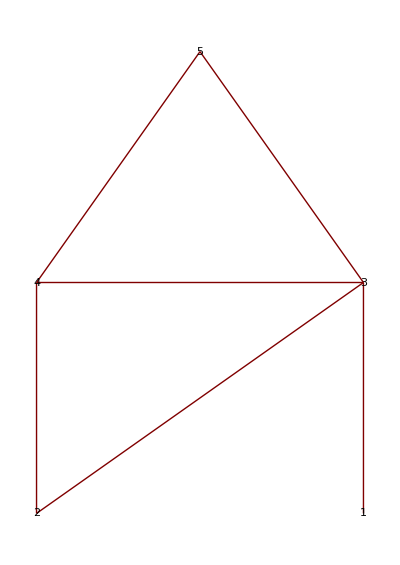

```mathematica
g={5->4,5->3,4->3,4->2,3->2,3->1};
TreePlot[g, VertexLabeling->True]
```

```mathematica
(* Iterative Method *)
```

```mathematica
Clear[i,n,a, b, c]
a = 0;
b = 1;
fibit[n_] := For[i=2,i≤n-1,i++,c=a+b; a = b;b = c]b;
First[fibit[7]]
```

8

```mathematica
(* Iterative Timing *)
```

```mathematica
timeit[n_] :=Timing[First[fibit[n]]]
timeit[4]
```

{0.000031,21}

```mathematica
(* Iterative Space *)
```

```mathematica
Clear[n]
spaceit[n_] := ByteCount[fibit[n]];
spaceit[15]
```

72

```mathematica
(* Iterative Time Plot *)
```

```mathematica
Clear[n];
timeplotit[n_] := ListLinePlot[{Table[{f, First[timeit[f]]}, {f, 1, n}]}];
Manipulate[timeplotit[n], {n, 0, 60}]
```

```mathematica
(* Iterative Space Plot *)
```

```mathematica
Clear[n];
spaceplotit[n_] := ListLinePlot[{Table[{f, spaceit[f]}, {f, 1, n}]}];
Manipulate[spaceplotit[n], {n, 0, 7}]
```

```mathematica
(* Iterative Tree Plot *)
```

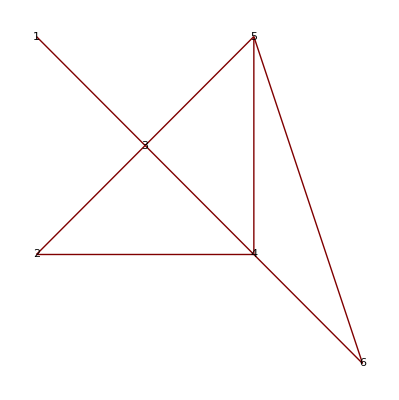

```mathematica
g={1->3,2->3,2->4,3->4,3->5,4->5,4->6,5->6};
TreePlot[g,Center, VertexLabeling->True]
```